```mathematica
{Cos[t],Sin[t]}/.t->0
```

{1,0}

```mathematica
ArcLength[{Cos[t],Sin[t]},{t,0,1}]
```

1

```mathematica
ArcLength[{Cos[t],Sin[t]},{t,0,2π}]
```

2 π

```mathematica
ArcLength[{x[t],y[t]},{t,a,b}]
```

Integrate[√(x'[t]^2+y'[t]^2),{t,a,b},Assumptions→a<b]

```mathematica
D[Integrate[√(x'[t]^2+y'[t]^2),{t,a,b},Assumptions->a<b], a]
```

-√(x'[a]^2+y'[a]^2)

```mathematica
ArcLength[{Cos[t],Sin[t]},{t,a,b}]
```

-a+b

```mathematica
ArcLength[{Cos[t],Sin[t]},{t,0,b}]
```

b

```mathematica
D[{Cos[t],Sin[t]},t]
```

{-Sin[t],Cos[t]}

```mathematica
Norm@{-Sin[t],Cos[t]}
```

√(Abs[Cos[t]]^2+Abs[Sin[t]]^2)

```mathematica
FullSimplify[√(Abs[Cos[t]]^2+Abs[Sin[t]]^2),t∈Reals]
```

1

```mathematica
a<b
```

a<b

```mathematica
Abs[a+b]≤Abs[a]+Abs[b]
```

Abs[a+b]≤Abs[a]+Abs[b]

```mathematica
FindInstance[Abs[a+b]≤Abs[a]+Abs[b],{a,b}]
```

{{a→0,b→0}}

```mathematica
Exp[Sin'[t]/Sin[t]]
```

ⅇ^Cot[t]

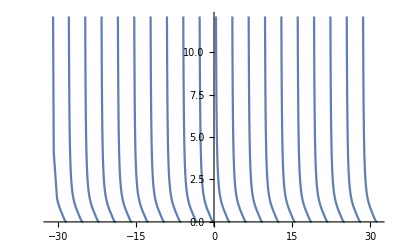

```mathematica
Plot[ⅇ^Cot[t],{t,-10 π,10 π}]
```

```mathematica
Exp[x]^2
```

ⅇ^(2 x)

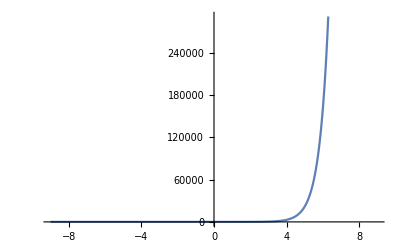

```mathematica
Plot[ⅇ^(2 x),{x,-9.,9.}]
```

```mathematica
Sin[x]^2
```

Sin[x]^2

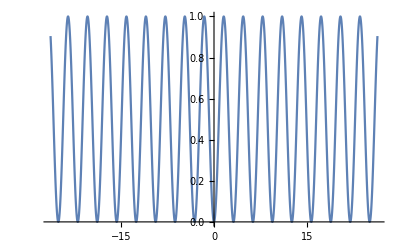

```mathematica
Plot[Sin[x]^2,{x,-26.389378290154262,26.389378290154262}]
```

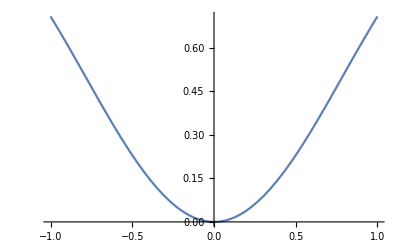

```mathematica
Plot[Sin[x]^2,{x,-1,1}]
```

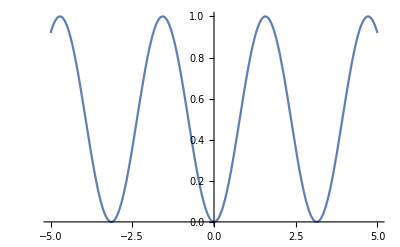

```mathematica
Plot[Sin[x]^2,{x,-5,5}]
```

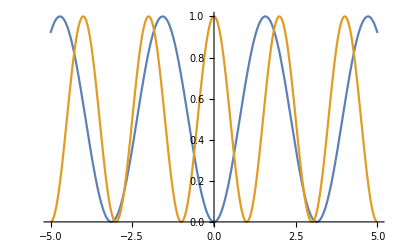

```mathematica
Plot[{Sin[x]^2,(1+Cos[π x])/2},{x,-5,5}]
```

```mathematica
(2(1-(1+Cos[π x])/2))+(3((1+Cos[π x])/2)+1)
```

1+2 (1+1/2 (-1-Cos[π x]))+3/2 (1+Cos[π x])

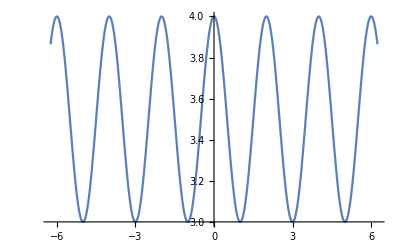

```mathematica
Plot[1+2 (1+1/2 (-1-Cos[π x]))+3/2 (1+Cos[π x]),{x,-6.24,6.24}]
```

```mathematica
((1-(1+Cos[π x])/2)/2)+(3((1+Cos[π x])/2)+1)
```

1+1/2 (1+1/2 (-1-Cos[π x]))+3/2 (1+Cos[π x])

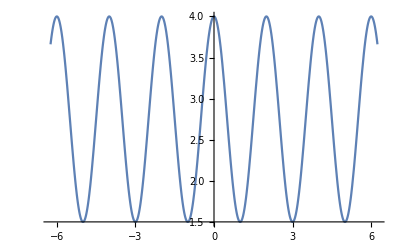

```mathematica
Plot[1+1/2 (1+1/2 (-1-Cos[π x]))+3/2 (1+Cos[π x]),{x,-6.24,6.24}]
```

```mathematica
(3(1-(1+Cos[π x])/2)+1)+(((1+Cos[π x])/2)/2)
```

1+3 (1+1/2 (-1-Cos[π x]))+1/4 (1+Cos[π x])

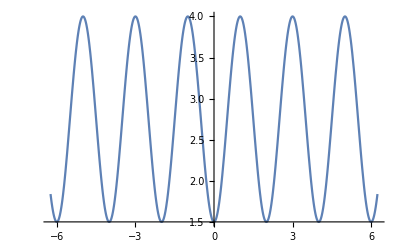

```mathematica
Plot[1+3 (1+1/2 (-1-Cos[π x]))+1/4 (1+Cos[π x]),{x,-6.24,6.24}]
```

```mathematica
((1-(1+Cos[π x])/2)(3x+1))+(((1+Cos[π x])/2)(x/2))
```

(1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x])

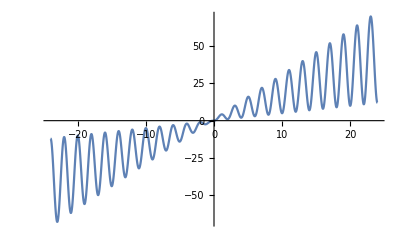

```mathematica
Plot[(1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]),{x,-24.,24.}]
```

```mathematica
(1-a)f[x]+a g[x]
```

(1-a) f[x]+a g[x]

```mathematica
Expand[(1-a) f[x]+a g[x]]
```

f[x]-a f[x]+a g[x]

```mathematica
Expand[(1-a[x])f[x]+a [x]g[x]]
```

f[x]-a[x] f[x]+a[x] g[x]

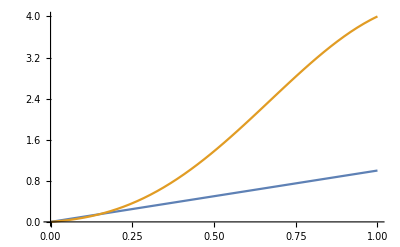

```mathematica
Plot[{x,(1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x])},{x,0,1}]
```

```mathematica
ArcLength[(1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]),{x,0,1}]
```

∫_0^1 √(1+(3 (1+1/2 (-1-Cos[π x]))+1/4 (1+Cos[π x])-1/4 π x Sin[π x]+1/2 π (1+3 x) Sin[π x])^2)ⅆx